## Load packages

```mathematica
SetDirectory[NotebookDirectory[]<>"/.."];
```

```mathematica
<<"PlotMatexFormatting.wl";
```

```mathematica
<<"ExtFileLoading.wl";
```

```mathematica
<<"ArrayManip.wl";
```

```mathematica
<<"FileNamings.wl";
```

## File reading constants

```mathematica
dirLog="./log/";
```

```mathematica
fNameFLstLstJld2="fNameFileLstJld2Lst.txt";
fNameFLstLst="fNameFileLstLst.txt";
fNameSaveParamLstLst="fNameSaveParamsLst.txt";
```

## Convergence check

### Adhoc testing

```mathematica
fNameLoopsNum="loopsNum_divNum_64_itNum_30000_cArea_1.0_cPerim_-1.0_beta_1_smart.jld2";
```

```mathematica
numBfieldLst=readJuliaVar[fNameLoopsNum,"numBfieldLst"];
```

```mathematica
numLinkLst=readJuliaVar[fNameLoopsNum,"numLinkLst"];
```

```mathematica
numLinkLst//Dimensions
```

{3,30000}

```mathematica
numBfieldLst//Dimensions
```

{3,30000}

```mathematica
bFieldLabLst=matexLstFunc[{"\\mathrm{iterations}","\\langle s \\rangle"},labMag];
```

```mathematica
bFieldLabLst
```

{-Graphics-,-Graphics-}

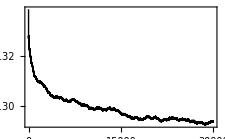

```mathematica
figBfieldHist=ListLinePlot[numBfieldLst⟦1⟧/64^3,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->8cm,PlotRangePadding->None,PlotStyle->lineStyleLst,FrameLabel->bFieldLabLst]
```

```mathematica
linkLabLst=matexLstFunc[{"\\mathrm{iterations}","\\langle \ell \\rangle"},labMag];
```

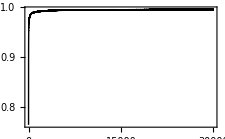

```mathematica
figLinkHist=ListLinePlot[numLinkLst⟦1⟧/64^3,PlotRange->All,PlotRange->Full,Frame->True,BaseStyle->texStyle,ImageSize->8cm,PlotRangePadding->None,PlotStyle->lineStyleLst,FrameLabel->linkLabLst]
```

```mathematica
Export["./figs/BfieldHistAB.pdf",figBfieldHist];
```

```mathematica
Export["./figs/linkHistAB.pdf",figLinkHist];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["./figs/BfieldHistAB.pdf"]]]
```

```mathematica
Directory[]
```

D:\Ohdraw.niL\OneDrive - UC San Diego\Programming\Julia\Modules

```mathematica
BfieldStartSampleLst=readJuliaVarDimFixed["loopsStartSample_divNum_64_itNum_100_cArea_0.6065306597126334_cPerim_-1.6487212707001282_beta_1_smartstaggeredCube.jld2","BfieldStartSampleLst"];
```

```mathematica
BfieldSampleLst=readJuliaVarSqDim["loopsSample_divNum_64_itNum_100_cArea_0.6065306597126334_cPerim_-1.6487212707001282_beta_1_smartstaggeredCube.jld2","BfieldSampleLst"];
```

```mathematica
BfieldSampleLst//Dimensions
```

{64,64,64,3,50}

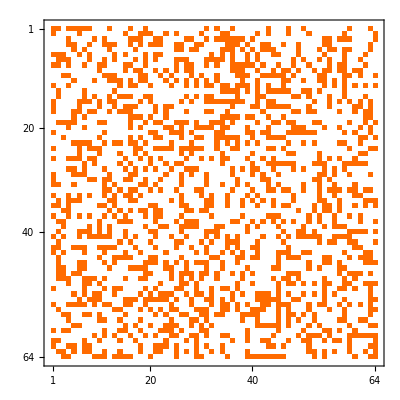

```mathematica
MatrixPlot[BfieldSampleLst⟦All,All,1,1,3⟧/.subBoolInt]
```

```mathematica
zakXTicks=Table[ii,{ii,0,1,0.2}];
zakYTicks=zakXTicks
```

{0.,0.2,0.4,0.6,0.8,1.}

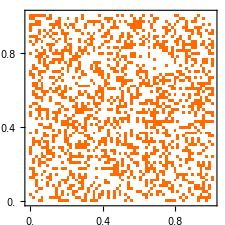

```mathematica
MatrixPlot[BfieldSampleLst⟦1,1,All,All,1⟧/.subBoolInt,PlotRangePadding->None,ImageSize->8cm,BaseStyle->texStyle,DataRange->{{0,1},{0,1}},FrameTicks->{{zakXTicks,None},{zakYTicks,None}}]
```

```mathematica
fNameLoopNum="loopsNum_divNum_64_itNum_100_cArea_0.6065306597126334_cPerim_-1.6487212707001282_beta_1_smartstaggeredCube.jld2";
```

```mathematica
numBfieldLst=readJuliaVarSqDim[fNameLoopNum,"numBfieldLst"];
```

```mathematica
numBfieldLst//Dimensions
```

{3,100}

```mathematica
numLinkLst=readJuliaVarSqDim[fNameLoopNum,"numLinkLst"];
```

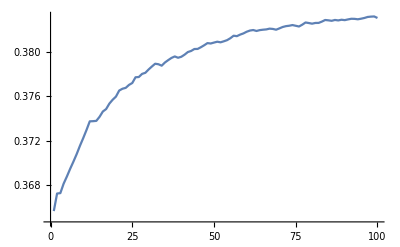

```mathematica
ListLinePlot[numBfieldLst⟦1⟧/64^3,PlotRange->All]
```

```mathematica
numLinkLst//Dimensions
```

{3,100}

```mathematica
64
```

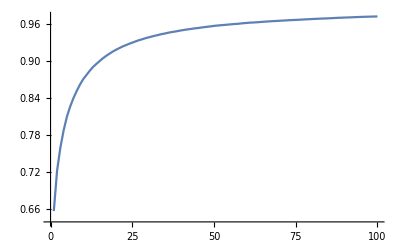

```mathematica
ListLinePlot[numLinkLst⟦1⟧/64^3,PlotRange->All]
```

```mathematica
fNameTest="loopsNum_divNum_64_itNum_100_cArea_0.6065306597126334_cPerim_-1.6487212707001282_beta_1_smart.jld2";
```

```mathematica
numLinkLstTest=readJuliaVarSqDim[fNameTest,"numLinkLst"];
```

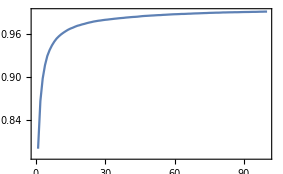

```mathematica
ListLinePlot[numLinkLstTest⟦1⟧/64^3,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

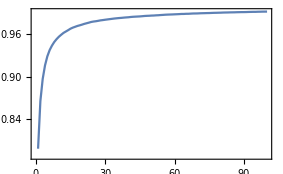

```mathematica
ListLinePlot[numLinkLstTest⟦1⟧/64^3,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

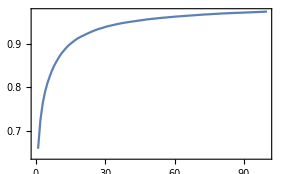

```mathematica
ListLinePlot[numLinkLstTest⟦1⟧/64^3,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

```mathematica
fSampleNameBeta10="loopsSample_divNum_64_itNum_100_cArea_6.065306597126334_cPerim_-16.48721270700128_beta_1_smart.jld2";
```

```mathematica
BfieldSampleLstTest10Staggered=readJuliaVarSqDim[fSampleNameBeta10,"BfieldSampleLst"];
```

```mathematica
BfieldSampleLstTest=readJuliaVarSqDim["loopsSample_divNum_64_itNum_100_cArea_0.6065306597126334_cPerim_-1.6487212707001282_beta_1_smart.jld2","BfieldSampleLst"];
```

```mathematica
BfieldSampleLstTest10//Dimensions
```

{100,3,64,64,64}

```mathematica
Clear[BfieldSampleLstTest]
```

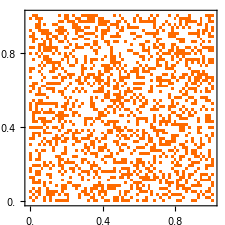

```mathematica
MatrixPlot[BfieldSampleLstTest⟦100,2,All,All,1⟧/.subBoolInt,PlotRangePadding->None,ImageSize->8cm,BaseStyle->texStyle,DataRange->{{0,1},{0,1}},FrameTicks->{{zakXTicks,None},{zakYTicks,None}}]
```

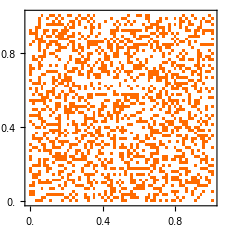

```mathematica
MatrixPlot[BfieldSampleLstTest⟦100,2,All,All,1⟧/.subBoolInt,PlotRangePadding->None,ImageSize->8cm,BaseStyle->texStyle,DataRange->{{0,1},{0,1}},FrameTicks->{{zakXTicks,None},{zakYTicks,None}}]
```

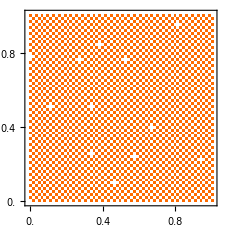

```mathematica
MatrixPlot[BfieldSampleLstTest10⟦100,1,All,All,1⟧/.subBoolInt,PlotRangePadding->None,ImageSize->8cm,BaseStyle->texStyle,DataRange->{{0,1},{0,1}},FrameTicks->{{zakXTicks,None},{zakYTicks,None}}]
```

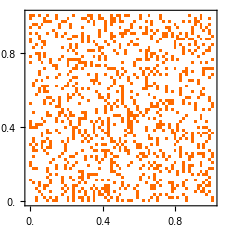

```mathematica
MatrixPlot[BfieldSampleLstTest10Staggered⟦10,3,All,All,1⟧/.subBoolInt,PlotRangePadding->None,ImageSize->8cm,BaseStyle->texStyle,DataRange->{{0,1},{0,1}},FrameTicks->{{zakXTicks,None},{zakYTicks,None}}]
```

```mathematica
fNameTest3="loopsNum_divNum_64_itNum_30000_cArea_1.0_cPerim_-1.0_beta_1_smart.jld2";
```

```mathematica
numLinkLstTestStg=readJuliaVarSqDim[fNameTest3,"numLinkLst"];
numBfieldLstTestStg=readJuliaVarSqDim[fNameTest3,"numBfieldLst"];
```

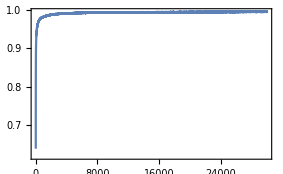

```mathematica
ListLinePlot[numLinkLstTestStg⟦1⟧/64^3,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

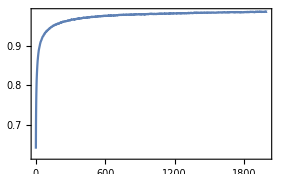

```mathematica
ListLinePlot[(numLinkLstTestStg⟦1⟧/64^3)⟦1;;2000⟧,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

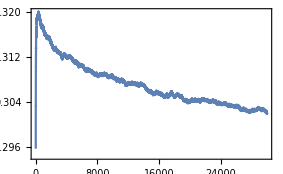

```mathematica
ListLinePlot[(numBfieldLstTestStg⟦1⟧/64^3),PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

### Parameter spread

```mathematica
fMainParam="loopsMC_params";
```

```mathematica
attrLstParamLst={"beta","cRatio","cFerroRatio","isInit0","sgnArea","sgnPerim"};
```

```mathematica
itNumLst={30000};
betaLst={0.2,1,3,10};
betaBase=1;
cRatioLst=Exp[Range[-2,2,0.4]];
cFerroRatioLst={0};
sgnAreaLst={1,-1};
sgnPerimLst={1,-1};
isInit0Lst={False,True};
divNumLst={64};
```

```mathematica
fModMethod="stag";
```

```mathematica
dirFig="./figs/";
```

```mathematica
nDim=3;
```

```mathematica
fNameFLstJld2=readTxtLastLine[dirLog<>fNameFLstLstJld2];
```

```mathematica
fNameArrLoopNum=reverseDims[readJuliaVar[fNameFLstJld2,"fNameArr"]];
```

```mathematica
fNameParams=readTxtLastLine[dirLog<>fNameSaveParamLstLst];
```

```mathematica
cAreaLst=reverseDims[readJuliaVar[fNameParams,"cAreaLst"]];
cPerimLst=reverseDims[readJuliaVar[fNameParams,"cPerimLst"]];
cFerroLst=reverseDims[readJuliaVar[fNameParams,"cFerroLst"]];
betaLst=reverseDims[readJuliaVar[fNameParams,"betaLst"]];
cRatioLst=reverseDims[readJuliaVar[fNameParams,"cRatioLst"]];
cFerroRatioLst=reverseDims[readJuliaVar[fNameParams,"cFerroRatioLst"]];
sgnAreaLst=reverseDims[readJuliaVar[fNameParams,"sgnAreaLst"]];
sgnPerimLst=reverseDims[readJuliaVar[fNameParams,"sgnPerimLst"]];
isInit0Lst=reverseDims[readJuliaVar[fNameParams,"isInit0Lst"]];
```

```mathematica
divNumLst=reverseDims[readJuliaVar[fNameParams,"divNumLst"]];
```

```mathematica
divNum=divNumLst⟦1⟧;
```

```mathematica
numGrd=divNum^3;
```

```mathematica
c2dLst={cAreaLst,cPerimLst};
```

```mathematica
c2dLstData=Transpose[c2dLst,{ArrayDepth[c2dLst]}~Join~Range[1,ArrayDepth[c2dLst]-1]];
```

```mathematica
dimRatio=2;
```

```mathematica
c2dLstDataRatioRaw=Transpose[c2dLstData,{ArrayDepth[cAreaLst]-1}~Join~{ArrayDepth[cAreaLst]}~Join~Range[dimRatio-1,ArrayDepth[cAreaLst]-2]~Join~{ArrayDepth[c2dLst]}];
```

```mathematica
c2dLstDataRatio=ArrayReshape[c2dLstDataRatioRaw,{Times@@Dimensions[c2dLstDataRatioRaw]⟦1;;ArrayDepth[c2dLstDataRatioRaw]-2⟧}~Join~Dimensions[c2dLstDataRatioRaw]⟦-2;;-1⟧];
```

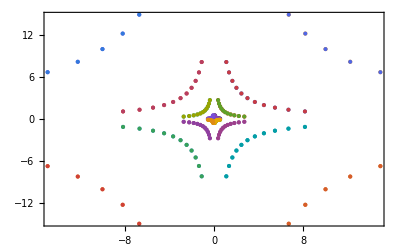

```mathematica
ListPlot[c2dLstDataRatio,PlotStyle->lineStyleLstDataThick,BaseStyle->texStyle,Frame->True]
```

```mathematica
fNameFLstFStrArr="fNameFileLstJld2Lst.txt";
```

```mathematica
dirLog<>fNameFLstFStrArr
```

./log/fNameFileLstJld2Lst.txt

```mathematica
fNameStrLst=readTxtLastLine[dirLog<>fNameFLstFStrArr];
```

```mathematica
fNameStrLstLoopNum=reverseDims[readJuliaVar[fNameStrLst,"fNameArr"]];
```

```mathematica
numBfieldLstArr=ConstantArray[0,Dimensions[fNameStrLstLoopNum]];
numLinkLstArr=ConstantArray[0,Dimensions[fNameStrLstLoopNum]];
```

```mathematica
numBfieldLstArr=ConstantArray[0,Dimensions[fNameArrLoopNum]];
numLinkLstArr=ConstantArray[0,Dimensions[fNameArrLoopNum]];
```

```mathematica
numBfieldLstArr=Table[readJuliaVar[fNameArrLoopNum⟦iIt,iDiv,iBeta,iCRatio,iFerro,iSgnArea,iSgnPerim,iInit⟧,"numBfieldLst"],{iIt,1},{iDiv,1},{iBeta,Length[betaLst]},{iCRatio,Length[cRatioLst]},{iFerro,Length[cFerroRatioLst]},{iSgnArea,Length[sgnAreaLst]},{iSgnPerim,Length[sgnPerimLst]},{iInit,Length[isInit0Lst]}];
```

```mathematica
numLinkLstArr=Table[readJuliaVar[fNameArrLoopNum⟦iIt,iDiv,iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim,iInit⟧,"numLinkLst"],{iIt,1},{iDiv,1},{iBeta,Length[betaLst]},{iCRatio,1,Length[cRatioLst]},{iCFerroRatio,Length[cFerroRatioLst]},{iSgnArea,Length[sgnAreaLst]},{iSgnPerim,Length[sgnPerimLst]},{iInit,Length[isInit0Lst]}];
```

```mathematica
fNameArrLoopNumTest=Table[fNameArrLoopNum⟦iIt,iDiv,iBeta,iCRatio,iFerro,iSgnArea,iSgnPerim,iInit⟧,{iIt,1},{iDiv,1},{iBeta,Length[betaLst]},{iCRatio,Length[cRatioLst]},{iFerro,Length[cFerroRatioLst]},{iSgnArea,Length[sgnAreaLst]},{iSgnPerim,Length[sgnPerimLst]},{iInit,Length[isInit0Lst]}];
```

```mathematica
numBfieldLstArr=Table[readJuliaVar[fNameStrLstLoopNum⟦iIt,iDiv,iBeta,iCRatio,iFerro,iSgnArea,iSgnPerim,iInit⟧,"numBfieldLst"],{iIt,1},{iDiv,1},{iBeta,Length[betaLst]},{iCRatio,Length[cRatioLst]},{iFerro,Length[cFerroRatioLst]},{iSgnArea,Length[sgnAreaLst]},{iSgnPerim,Length[sgnPerimLst]},{iInit,Length[isInit0Lst]}];
```

```mathematica
fNameStrLstLoopNumTest=Table[fNameStrLstLoopNum⟦iIt,iDiv,iBeta,iCRatio,iFerro,iSgnArea,iSgnPerim,iInit⟧,{iIt,1},{iDiv,1},{iBeta,Length[betaLst]},{iCRatio,Length[cRatioLst]},{iFerro,Length[cFerroRatioLst]},{iSgnArea,Length[sgnAreaLst]},{iSgnPerim,Length[sgnPerimLst]},{iInit,Length[isInit0Lst]}];
```

```mathematica
itCut=10000;
```

### Start plotting

```mathematica
dimLabLst={"x","y","z"};
```

```mathematica
xyLabLnkLst=Table[matexLstFunc[{"\\mathrm{iteration}","\\langle \\ell_"<>dimLabLst⟦iDim⟧<>" \\rangle"},labMag],{iDim,1,nDim}];
xyLabBfieldLst=Table[matexLstFunc[{"\\mathrm{iteration}","\\langle s_"<>dimLabLst⟦iDim⟧<>" \\rangle"},labMag],{iDim,1,nDim}];
```

```mathematica
xyLabLnkLst
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
xyLabBfieldLst
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
titleVarLstRaw={"c_A","c_L", "c_F"};
```

```mathematica
titleFigLstRaw=Table[
Module[{valLst},
valLst={cAreaLst⟦iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim⟧,cPerimLst⟦iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim⟧,cFerroLst⟦iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim⟧};
titleParamLstGen[titleVarLstRaw,If[#==0.0,0,NumberForm[#,{∞,3}]]&/@valLst]
],
{iBeta,Length[betaLst]},{iCRatio,Length[cRatioLst]},{iCFerroRatio,Length[cFerroRatioLst]},{iSgnArea,Length[sgnAreaLst]},{iSgnPerim,Length[sgnPerimLst]}];
```

```mathematica
titleFigLst=matexLstFunc[titleFigLstRaw,labMag];
```

```mathematica
pltNumLstFunc[numLst_,titleStr_,xyLabStr_,xCut_]:=
ListPlot[numLst⟦1;;xCut⟧/numGrd,PlotRange->All,Frame->True,BaseStyle->texStyle,FrameLabel->xyLabStr,PlotLabel->titleStr,PlotStyle->lineStyleLstDataThick,ImageSize->8cm,PlotRangePadding->None];
```

```mathematica
pltLstNumBfield=Table[pltNumLstFunc[numBfieldLstArr⟦iIt,iDiv,iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim,iInit0,iDim⟧,titleFigLst⟦iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim⟧,xyLabBfieldLst⟦iDim⟧,itCut],{iIt,1},{iDiv,1},{iBeta,Length[betaLst]},{iCRatio,Length[cRatioLst]},{iCFerroRatio,Length[cFerroRatioLst]},{iSgnArea,Length[sgnAreaLst]},{iSgnPerim,Length[sgnPerimLst]},{iInit0,Length[isInit0Lst]},{iDim,3}];
```

```mathematica
pltLstNumLink=Table[pltNumLstFunc[numLinkLstArr⟦iIt,iDiv,iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim,iInit0,iDim⟧,titleFigLst⟦iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim⟧,xyLabLnkLst⟦iDim⟧,itCut],{iIt,1},{iDiv,1},{iBeta,Length[betaLst]},{iCRatio,Length[cRatioLst]},{iCFerroRatio,Length[cFerroRatioLst]},{iSgnArea,Length[sgnAreaLst]},{iSgnPerim,Length[sgnPerimLst]},{iInit0,Length[isInit0Lst]},{iDim,3}];
```

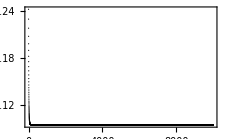

```mathematica
pltLstNumBfield⟦1,1,3,1,1,1,1,1,3⟧
```

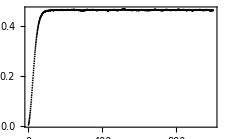

```mathematica
pltNumLstFunc[numBfieldLstArr⟦1,1,1,1,1,1,1,2,1⟧,1000]
```

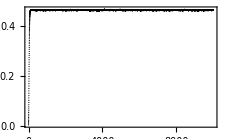

```mathematica
pltLstNumBfield⟦1,1,1,1,1,1,1,2,3⟧
```

```mathematica
pltTest1=pltNumLstFunc[numBfieldLstArr⟦1,1,1,1,1,1,2,1,1⟧,10000];
```

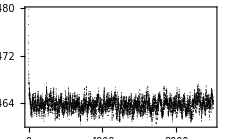

```mathematica
Print[pltTest1]
```

```mathematica
numLinkLstArr//Dimensions
```

{1,1,4,11,1,2,2,2,3,30000}

```mathematica
xyLabLnk
```

{-Graphics-,-Graphics-}

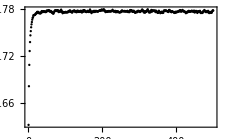

```mathematica
ListPlot[numLinkLstArr⟦1,1,1,1,1,1,2,1,1,1;;500⟧/numGrd,PlotRange->All,Frame->True,BaseStyle->texStyle,FrameLabel->xyLabLnk,PlotStyle->lineStyleLstDataThick,ImageSize->8cm,PlotRangePadding->None]
```

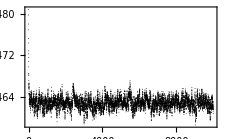

```mathematica
ListPlot[numBfieldLstArr⟦1,1,1,1,1,1,1,1,1,1;;10000⟧/numGrd,PlotRange->All,Frame->True,BaseStyle->texStyle,FrameLabel->xyLabLnk,PlotStyle->lineStyleLstDataThick,ImageSize->8cm,PlotRangePadding->None]
```

```mathematica
fMainLoopMCFig="loopsMC";
fMainLoopMCFigBfield=fMainLoopMCFig<>"Bfield";
fMainLoopMCFigLink=fMainLoopMCFig<>"Link";
```

```mathematica
attrLstLoopsMCFig={"cArea","cPerim","isInit0","iDim","itCut"};
```

```mathematica
Do[
Module[{valLstFig,fNameFig},
valLstFig={cAreaLst⟦iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim⟧,cPerimLst⟦iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim⟧,isInit0Lst⟦iInit0⟧,iDim,itCut};
fNameFig=fNameFun[fMainLoopMCFigBfield,attrLstLoopsMCFig,valLstFig,fModMethod,pdfType];
Export[dirFig<>fNameFig,pltLstNumBfield⟦iIt,iDiv,iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim,iInit0,iDim⟧];
],
{iIt,1},{iDiv,1},{iBeta,Length[betaLst]},{iCRatio,Length[cRatioLst]},{iCFerroRatio,Length[cFerroRatioLst]},{iSgnArea,Length[sgnAreaLst]},{iSgnPerim,Length[sgnPerimLst]},{iInit0,Length[isInit0Lst]},{iDim,nDim}]
```

```mathematica
Do[
Module[{valLstFig,fNameFig},
valLstFig={cAreaLst⟦iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim⟧,cPerimLst⟦iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim⟧,isInit0Lst⟦iInit0⟧,iDim,itCut};
fNameFig=fNameFun[fMainLoopMCFigLink,attrLstLoopsMCFig,valLstFig,fModMethod,pdfType];
Export[dirFig<>fNameFig,pltLstNumLink⟦iIt,iDiv,iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim,iInit0,iDim⟧];
],
{iIt,1},{iDiv,1},{iBeta,Length[betaLst]},{iCRatio,Length[cRatioLst]},{iCFerroRatio,Length[cFerroRatioLst]},{iSgnArea,Length[sgnAreaLst]},{iSgnPerim,Length[sgnPerimLst]},{iInit0,Length[isInit0Lst]},{iDim,nDim}]
```

```mathematica
Do[
Module[{valLstFig,fNameFig},
valLstFig={cAreaLst⟦iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim⟧,cPerimLst⟦iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim⟧,isInit0Lst⟦iInit0⟧,iDim,itCut};
fNameFig=fNameFun[fMainLoopMCFigBfield,attrLstLoopsMCFig,valLstFig,fModMethod,pdfType];
Export[dirFig<>fNameFig,pltLstNumBfield⟦iIt,iDiv,iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim,iInit0,iDim⟧];
Print[fNameFig]
],
{iIt,1},{iDiv,1},{iBeta,1},{iCRatio,1},{iCFerroRatio,1},{iSgnArea,1},{iSgnPerim,1},{iInit0,Length[isInit0Lst]},{iDim,nDim}]
```

loopsMCBfield_cArea_0.0735759_cPerim_0.543656_isInit0_False_iDim_1_itCut_10000_stag.pdf

loopsMCBfield_cArea_0.0735759_cPerim_0.543656_isInit0_False_iDim_2_itCut_10000_stag.pdf

loopsMCBfield_cArea_0.0735759_cPerim_0.543656_isInit0_False_iDim_3_itCut_10000_stag.pdf

loopsMCBfield_cArea_0.0735759_cPerim_0.543656_isInit0_True_iDim_1_itCut_10000_stag.pdf

loopsMCBfield_cArea_0.0735759_cPerim_0.543656_isInit0_True_iDim_2_itCut_10000_stag.pdf

loopsMCBfield_cArea_0.0735759_cPerim_0.543656_isInit0_True_iDim_3_itCut_10000_stag.pdf

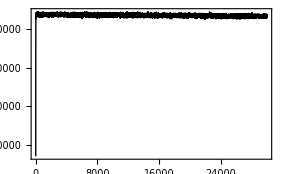

```mathematica
ListLinePlot[numLinkLst1⟦3⟧,PlotRange->All,Frame->True,BaseStyle->texStyle,PlotStyle->lineStyleLstDataThick,PlotRangePadding->None,ImageSize->10cm]
```

```mathematica
{t1,b1}=AbsoluteTiming[Do[
Module[{valLstFig,fNameFig},
valLstFig={cAreaLst⟦iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim⟧,cPerimLst⟦iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim⟧,isInit0Lst⟦iInit0⟧,iDim,itCut};
fNameFig=fNameFun[fMainLoopMCFigLink,attrLstLoopsMCFig,valLstFig,fModMethod,pdfType];
Export[dirFig<>fNameFig,pltLstNumLink⟦iIt,iDiv,iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim,iInit0,iDim⟧];
],
{iIt,1},{iDiv,1},{iBeta,1},{iCRatio,1},{iCFerroRatio,Length[cFerroRatioLst]},{iSgnArea,1},{iSgnPerim,Length[sgnPerimLst]},{iInit0,Length[isInit0Lst]},{iDim,nDim}]];t1
```

10.8402

```mathematica
valLstFig=Table[{cAreaLst⟦iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim⟧,cPerimLst⟦iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim⟧,isInit0Lst⟦iInit0⟧,iDim},{iBeta,Length[betaLst]},{iCRatio,Length[cRatioLst]},{iCFerroRatio,Length[cFerroRatioLst]},{iSgnArea,Length[sgnAreaLst]},{iSgnPerim,Length[sgnPerimLst]},{iInit0,Length[isInit0Lst]},{iDim,1,nDim}];
```

```mathematica
{t1,b1}=AbsoluteTiming[Export[dirFig<>"testFigLoopsMC.pdf",pltTest1]];t1
```

0.907217

```mathematica
pltLstNumBfield//Dimensions
```

{1,1,4,11,1,2,2,2,3}

```mathematica
Times@@Dimensions[pltLstNumBfield]
```

1056

```mathematica
1056/60//N
```

17.6

```mathematica
Length[pltLstNumBfield]
```

1

## Misc tests

```mathematica
fNameFLstLstJld2
```

fNameFileLstJld2Lst.txt

```mathematica
fNameArr//Dimensions
```

{1,1,4,11,1,2,2,2}

```mathematica
fNameArr⟦1,1,1,1,1,1,1,1⟧
```

loopsNum_divNum_64_itNum_30000_cArea_0.07357588823428847_cPerim_0.5436563656918091_beta_1_stag.jld2

```mathematica
fNameParams
```

loopsMC_params_beta_[0.2, 10.0]_cRatio_[0.135, 7.389]_cFerroRatio_[0, 0]_isInit0_Bool[0, 1]_sgnArea_[1, -1]_sgnPerim_[1, -1]_smart_upStagCube.jld2

```mathematica
fNameFLstFStrArr//Dimensions
```

{1,1,4,11,1,2,2,2}

```mathematica
numBfieldLstArr//Dimensions
```

{1,1,4,11,1,2,2,2}

```mathematica
fNameArrLoopNumTest//Dimensions
```

{1,1,4,11,1,2,2,2}

```mathematica
fNameArrLoopNumTest
```

```mathematica
numBfieldLstArr//Dimensions
```

{1,1,4,11,1,2,2,2,3,30000}

```mathematica
divNum
```

64

```mathematica
numGrd
```

262144

```mathematica
fMainLoopMCFigLink
```

loopsMCLink

```mathematica
fNameParams
```

loopsMC_params_beta_[0.2, 10.0]_cRatio_[0.135, 7.389]_cFerroRatio_[0, 0]_isInit0_Bool[0, 1]_sgnArea_[1, -1]_sgnPerim_[1, -1]_stag.jld2

```mathematica
cAreaLst//Dimensions
```

{4,11,1,2,2}

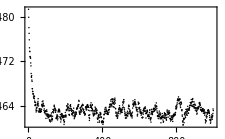

```mathematica
pltNumLstFunc[numBfieldLstArr⟦1,1,1,1,1,1,1,1,3⟧,titleFigLst⟦1,1,1,1,1⟧,xyLabBfieldLst⟦3⟧,1000]
```

```mathematica
a
```

```mathematica
asdf
```

```mathematica
adf
```